```mathematica
ClearAll["Global`*"]
```

```mathematica
Needs["ErrorBarPlots`"]
```

3

2048

2048

2048

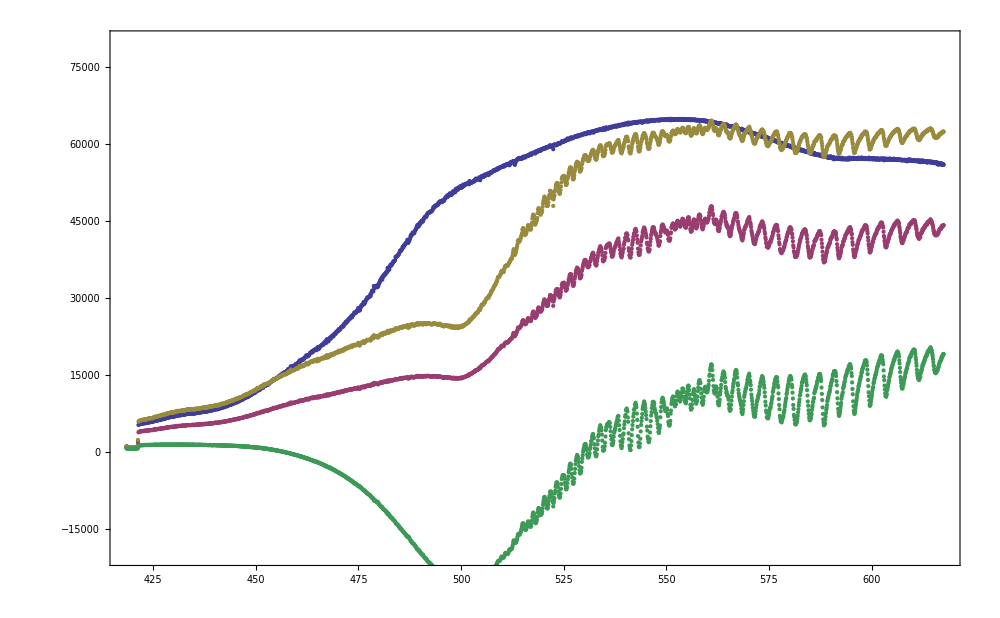

```mathematica
names={"03_Halogen_ngg10.txt","04_I2_ngg10_10ms.txt","04_I2_ngg10_17ms.txt"};
imp=Table[Import[ParentDirectory[NotebookDirectory[]]<>"\\data\\"<>names[[i]],"Table",NumberPoint->","],{i,1,Length[names]}];
data=Table[Drop[imp[[i]],17],{i,1,3}];
data=Table[Drop[data[[i]],-1],{i,1,3}];
Length[data]
Length[data[[1]]]
Length[data[[2]]]
Length[data[[3]]]
datab=data;
datab[[2,All,2]]=1.7*data[[2,All,2]];
datab[[3,All,2]]=datab[[3,All,2]]-data[[1,All,2]];
datab[[2,All,2]]=datab[[2,All,2]]-data[[1,All,2]];
ListPlot[{data[[1]],data[[2]],data[[3]],datab[[2]]},PlotRange->{-20000,80000},ImageSize->1000,Frame->True]
```

181

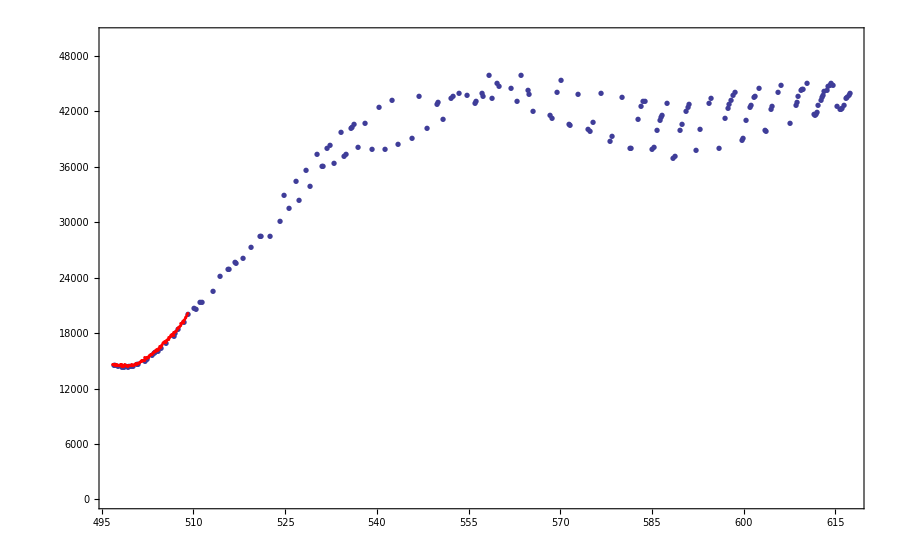

```mathematica
l=Drop[data[[2]],700];
minima={};
Δ=1;
For[i=Δ+1,i≤Length[l]-(Δ+1),i++,
If[FreeQ[
Table[l[[i+n,2]]≥ l[[i,2]],{n,-Δ,Δ}],
False],
{minima=Append[minima,Append[l[[i]],i]]}
]
]
Length[minima]
Show[
ListPlot[{Drop[minima,None,-1],x1b},PlotRange->{Automatic,{0,50000}},ImageSize->900,Frame->True,PlotMarkers->{Automatic,7}],
ListPlot[l,PlotMarkers->{Automatic,2},PlotStyle->Red]
]
```

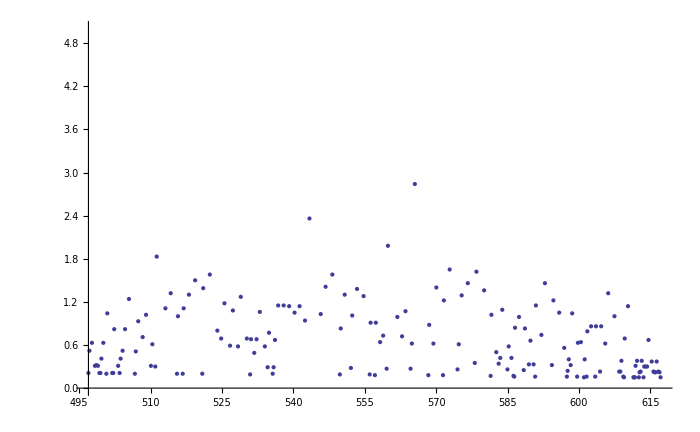

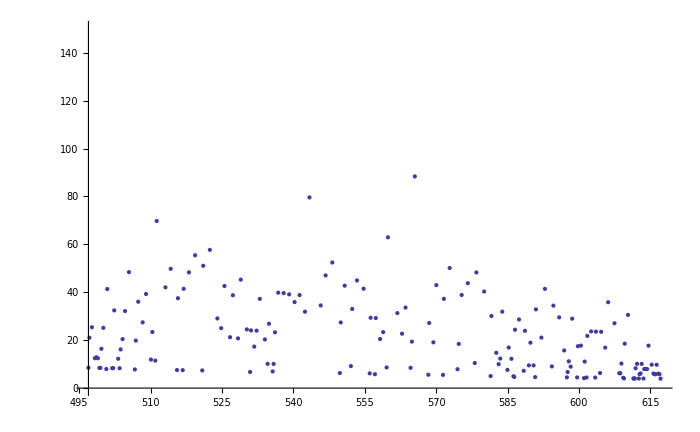

```mathematica
x1=Table[{minima[[i,1]],minima[[i+1,1]]-minima[[i,1]]},{i,1,Length[minima]-1}];
x1b=x1;
x1b[[All,2]]=9000*x1b[[All,2]];
ListPlot[x1,ImageSize->700,PlotRange->{0,5}]
x2=Table[{minima[[i,1]],1/(minima[[i,1]]*10^-7)-1/(minima[[i+1,1]]*10^-7)},{i,1,Length[minima]-1}];
ListPlot[x2,ImageSize->700,PlotRange->{0,150}]
```

```mathematica
minima
```

{{496.95,14511.2,3},{497.16,14493.1,5},{497.68,14387.7,10},{498.31,14354.2,16},{498.62,14338.7,19},{498.94,14412.8,22},{499.25,14347.6,25},{499.46,14431.3,27},{499.67,14425.1,29},{500.08,14419.9,33},{500.71,14596.2,39},{500.91,14671.1,41},{501.95,14979.6,51},{502.16,15182.3,53},{502.37,15218.7,55},{503.19,15633.1,63},{503.5,15811.8,66},{503.71,15962.4,68},{504.12,16081.5,72},{504.64,16340.,77},{505.46,16968.2,85},{506.7,17715.9,97},{506.9,17987.2,99},{507.41,18423.5,104},{508.34,19142.8,113},{509.05,20006.5,120},{510.07,20665.9,130},{510.38,20648.4,133},{510.99,21331.3,139},{511.29,21341.5,142},{513.12,22594.8,160},{514.23,24139.3,171},{515.55,24918.6,184},{515.75,24965.6,186},{516.75,25676.8,196},{516.95,25534.3,198},{518.06,26152.2,209},{519.36,27342.,222},{520.86,28514.8,237},{521.06,28510.6,239},{522.45,28514.1,253},{524.03,30137.6,269},{524.83,32899.8,277},{525.52,31489.5,284},{526.7,34405.9,296},{527.29,32406.1,302},{528.37,35653.1,313},{528.95,33866.4,319},{530.22,37301.,332},{530.91,36006.5,339},{531.1,36073.6,341},{531.78,37956.9,348},{532.27,38313.6,353},{532.95,36370.8,360},{534.01,39752.5,371},{534.59,37163.,377},{534.88,37365.,380},{535.65,40175.3,388},{535.85,40319.6,390},{536.14,40552.3,393},{536.81,38085.2,400},{537.96,40735.8,412},{539.11,37937.6,424},{540.25,42392.4,436},{541.3,37900.8,447},{542.44,43187.5,459},{543.38,38435.5,469},{545.74,39060.8,494},{546.77,43673.7,505},{548.18,40202.9,520},{549.76,42767.4,537},{549.95,43011.8,539},{550.78,41168.5,548},{552.08,43372.7,562},{552.36,43579.,565},{553.37,43897.2,576},{554.75,43685.8,591},{556.03,42904.3,605},{556.22,43105.3,607},{557.13,43905.9,617},{557.31,43573.6,619},{558.22,45901.3,629},{558.86,43389.9,636},{559.59,45029.1,644},{559.86,44733.5,647},{561.84,44442.5,669},{562.83,43045.1,680},{563.55,45882.2,688},{564.62,44223.9,700},{564.89,43824.3,703},{565.51,42056.3,710},{568.35,41535.7,742},{568.53,41244.5,744},{569.41,44092.,754},{570.03,45355.7,761},{571.43,40615.4,777},{571.61,40516.4,779},{572.83,43811.5,793},{574.48,40008.3,812},{574.74,39839.5,815},{575.35,40850.6,822},{576.64,43944.7,837},{578.1,38753.1,854},{578.45,39297.2,858},{580.07,43535.7,877},{581.43,38001.2,893},{581.6,38001.,895},{582.62,41146.5,907},{583.12,42581.1,913},{583.46,43081.8,917},{583.88,43096.9,922},{584.97,37887.3,935},{585.23,38104.4,938},{585.81,39924.1,945},{586.23,41084.,950},{586.4,41305.4,952},{586.56,41615.,954},{587.4,42899.4,964},{588.39,36955.,976},{588.64,37136.5,979},{589.47,39982.8,989},{589.8,40644.7,993},{590.46,42020.4,1001},{590.79,42447.1,1005},{590.95,42797.6,1007},{592.1,37770.3,1021},{592.84,40073.3,1030},{594.3,42920.7,1048},{594.62,43406.6,1052},{595.84,37995.2,1067},{596.89,41211.6,1080},{597.45,42312.6,1087},{597.61,42747.,1089},{597.85,43218.5,1092},{598.25,43732.4,1097},{598.57,44039.5,1101},{599.61,38881.9,1114},{599.77,39063.6,1116},{600.4,40990.9,1124},{601.04,42451.,1132},{601.19,42675.7,1134},{601.59,43475.8,1139},{601.75,43646.2,1141},{602.54,44502.7,1151},{603.4,39959.7,1162},{603.56,39868.5,1164},{604.42,42207.9,1175},{604.65,42550.3,1178},{605.51,44053.6,1189},{606.13,44764.6,1197},{607.45,40721.4,1214},{608.45,42654.2,1227},{608.68,42939.2,1230},{608.91,43588.8,1233},{609.29,44274.7,1238},{609.45,44350.5,1240},{609.6,44419.,1242},{610.29,45005.8,1251},{611.43,41704.9,1266},{611.58,41522.3,1268},{611.73,41730.1,1270},{611.88,41882.4,1272},{612.19,42698.1,1276},{612.57,43236.9,1281},{612.72,43492.3,1283},{612.94,43787.9,1286},{613.17,44143.4,1289},{613.55,44299.7,1294},{613.7,44685.2,1296},{614.,44851.9,1300},{614.3,44992.5,1304},{614.6,44869.3,1308},{615.27,42572.,1317},{615.64,42203.3,1322},{615.87,42256.1,1325},{616.09,42372.2,1328},{616.31,42653.8,1331},{616.68,43426.5,1336},{616.91,43476.4,1339},{617.13,43778.4,1342},{617.28,43923.9,1344}}

{{545.27,40795.2},{547.43,42538.1},{549.95,43011.8},{552.36,43579.},{554.75,43685.8},{557.31,43573.6},{559.86,44733.5},{562.74,43093.5},{565.51,42056.3},{568.53,41244.5},{571.61,40516.4},{574.74,39839.5},{578.1,38753.1},{581.6,38001.},{584.97,37887.3},{588.39,36955.},{592.1,37770.3},{595.84,37995.2},{599.77,39063.6},{603.56,39868.5},{607.45,40721.4},{611.58,41522.3}}

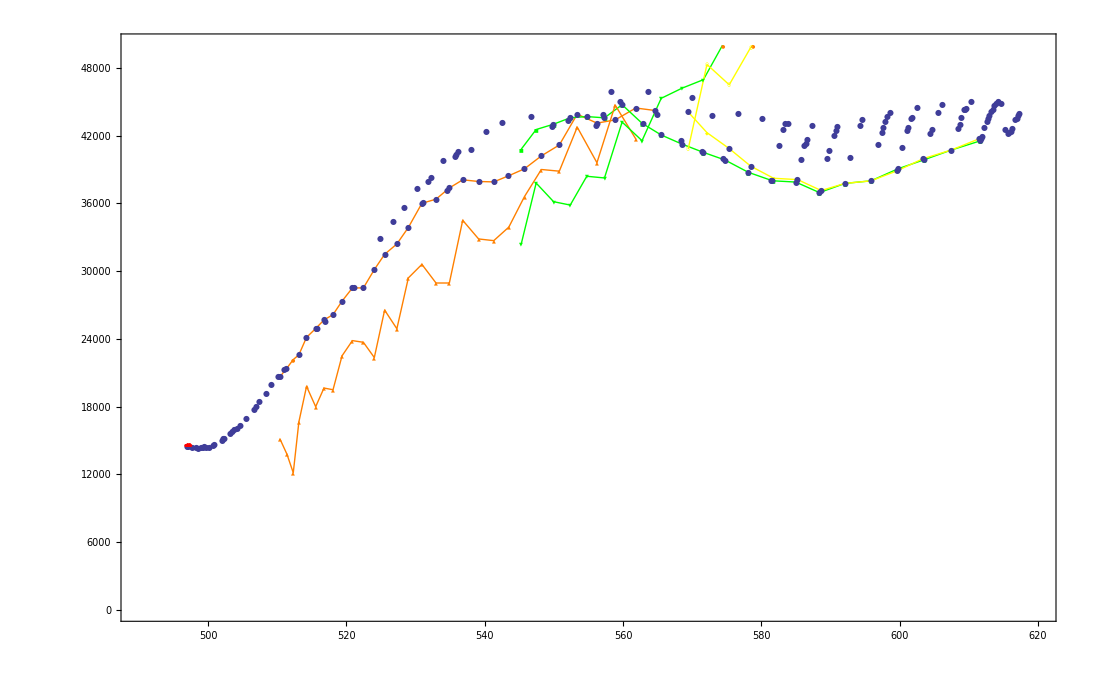

```mathematica
(*Macht Plotliste aus minima, mit Tooltips*)
mintips=Table[Tooltip[{minima[[i,1]],minima[[i,2]]},{minima[[i,3]],minima[[i,1]]}],{i,1,Length[minima]}];

posprog1={133,143,152,160,171,184,196,209,222,237,253,269,284,302,319,339,360,380,400,424,447,470,494,520,548,576,607,636,669,700(*,737,771,808,844,883,922,964,1007,1052,1101,1151,1197,1251*)};
posprog1=Sort[posprog1];
posprog1b=Table[{i},{i,posprog1}];

posprog2={489,512,539,565,591,619,647,679,710,744,779,815,854,895,935,976,1021,1067,1116,1164,1214,1268};
posprog2=Sort[posprog2];
posprog2b=Table[{i},{i,posprog2}];

posprog3={754,785,822,858,897,938,979,1021,1067,1114,1162,1214,1266};
posprog3=Sort[posprog3];
posprog3b=Table[{i},{i,posprog3}];

(* Einzelne Punkte aus großer Datenliste nehmen *)
prog1=Extract[l,posprog1b];
prog2=Extract[l,posprog2b]
prog3=Extract[l,posprog3b];

(*Differez berechnen, multiplizieren für Anzeige*)
Δprog1=Table[{prog1[[i,1]],prog1[[i+1,1]]-prog1[[i,1]]},{i,1,Length[prog1]-1}];
Δprog1h=Δprog1;
Δprog1h[[All,2]]=15000*Δprog1h[[All,2]];

Δprog2=Table[{prog2[[i,1]],prog2[[i+1,1]]-prog2[[i,1]]},{i,1,Length[prog2]-1}];
Δprog2h=Δprog2;
Δprog2h[[All,2]]=15000*Δprog2h[[All,2]];

Δprog3=Table[{prog3[[i,1]],prog3[[i+1,1]]-prog3[[i,1]]},{i,1,Length[prog3]-1}];
Δprog3h=Δprog3;
Δprog3h[[All,2]]=15000*Δprog3h[[All,2]];

Show[ListPlot[{prog1,prog2,prog3,Δprog1h,Δprog2h,Δprog3h},Frame->True,Joined->True,PlotMarkers->{Automatic,5},PlotRange->{{490,620},{0,50000}},ImageSize->1100,PlotStyle->{Orange,Green,Yellow,Orange,Green,Yellow}],
ListPlot[mintips,PlotMarkers->{Automatic,8}],
ListPlot[l,PlotMarkers->{Automatic,2},PlotStyle->Red,Joined->False]]
```

# Vergleich mit Literaturwerten aus Paper

```mathematica
i=Import[NotebookDirectory[]<>"\\iod lit.txt","Table"]
i//TableForm
10^7/i[[All,2]]
prog1[[All,1]]
10^7/i[[All,4]]
prog2[[All,1]]-0.3
10^7/Drop[i,7][[All,6]]
prog3[[All,1]]-0.3
```

{{1,18559.7,16,18350.7,209.},{2,18484.5,17,18275.2,209.3},{3,18408.3,18,18195.4,212.9},{4,18330.5,19,18115.1,215.4},{5,18246.5,20,18029.7,216.8},{8,18162.,21,17948.,214.},{7,18075.8,22,17863.9,211.9},{8,17987.6,23,17777.7,31,17569.6,208.9,208.1},{9,17898.2,24,17688.9,32,17477.1,209.3,211.8},{10,17810.2,25,17598.2,33,17387.1,212.,211.1},{11,17717.8,26,17504.3,34,17292.4,213.6,211.9},{12,17621.9,27,17407.,35,17196.9,214.9,210.1},{13,17524.2,28,17309.6,36,17098.4,214.6,211.2},{14,17425.3,29,17211.7,37,16999.2,213.6,212.5},{15,17323.5,30,17108.6,38,16985.8,214.9,212.8}}

1 | 18559.7 | 16 | 18350.7 | 209. |  |  | 
2 | 18484.5 | 17 | 18275.2 | 209.3 |  |  | 
3 | 18408.3 | 18 | 18195.4 | 212.9 |  |  | 
4 | 18330.5 | 19 | 18115.1 | 215.4 |  |  | 
5 | 18246.5 | 20 | 18029.7 | 216.8 |  |  | 
8 | 18162. | 21 | 17948. | 214. |  |  | 
7 | 18075.8 | 22 | 17863.9 | 211.9 |  |  | 
8 | 17987.6 | 23 | 17777.7 | 31 | 17569.6 | 208.9 | 208.1
9 | 17898.2 | 24 | 17688.9 | 32 | 17477.1 | 209.3 | 211.8
10 | 17810.2 | 25 | 17598.2 | 33 | 17387.1 | 212. | 211.1
11 | 17717.8 | 26 | 17504.3 | 34 | 17292.4 | 213.6 | 211.9
12 | 17621.9 | 27 | 17407. | 35 | 17196.9 | 214.9 | 210.1
13 | 17524.2 | 28 | 17309.6 | 36 | 17098.4 | 214.6 | 211.2
14 | 17425.3 | 29 | 17211.7 | 37 | 16999.2 | 213.6 | 212.5
15 | 17323.5 | 30 | 17108.6 | 38 | 16985.8 | 214.9 | 212.8

{538.802,540.994,543.233,545.539,548.05,550.6,553.226,555.939,558.715,561.476,564.404,567.476,570.639,573.878,577.251}

{510.38,511.39,512.31,513.12,514.23,515.55,516.75,518.06,519.36,520.86,522.45,524.03,525.52,527.29,528.95,530.91,532.95,534.88,536.81,539.11,541.3,543.48,545.74,548.18,550.78,553.37,556.22,558.86,561.84,564.62}

{544.938,547.19,549.589,552.026,554.64,557.165,559.788,562.502,565.326,568.24,571.288,574.482,577.714,581.,584.501}

{544.97,547.13,549.65,552.06,554.45,557.01,559.56,562.44,565.21,568.23,571.31,574.44,577.8,581.3,584.67,588.09,591.8,595.54,599.47,603.26,607.15,611.28}

{569.165,572.177,575.139,578.289,581.5,584.85,588.263,588.727}

{569.11,571.83,575.05,578.15,581.47,584.93,588.34,591.8,595.54,599.31,603.1,607.15,611.13}

# Export

```mathematica
e1=Table[{posprog1[[i]],prog1[[i,1]],prog1[[i,2]]},{i,1,Length[posprog1]}];
e2=Table[{posprog2[[i]],prog2[[i,1]],prog2[[i,2]]},{i,1,Length[posprog2]}];
e3=Table[{posprog3[[i]],prog3[[i,1]],prog3[[i,2]]},{i,1,Length[posprog3]}];
Export[ParentDirectory[NotebookDirectory[]]<>"\\data\\"<>"prog1.txt",e1,"Table"]
Export[ParentDirectory[NotebookDirectory[]]<>"\\data\\"<>"prog2.txt",e2,"Table"]
Export[ParentDirectory[NotebookDirectory[]]<>"\\data\\"<>"prog3.txt",e3,"Table"]
```

C:\fpgithub\0916-I2\data\prog1.txt

C:\fpgithub\0916-I2\data\prog2.txt

C:\fpgithub\0916-I2\data\prog3.txt

```mathematica
Export[ParentDirectory[NotebookDirectory[]]<>"\\data\\"<>"prog1.txt",prog1,"Table"]
Export[ParentDirectory[NotebookDirectory[]]<>"\\data\\"<>"prog2.txt",prog2,"Table"]
Export[ParentDirectory[NotebookDirectory[]]<>"\\data\\"<>"prog3.txt",prog3,"Table"]
```

C:\fpgithub\0916-I2\data\prog1.txt

C:\fpgithub\0916-I2\data\prog2.txt

C:\fpgithub\0916-I2\data\prog3.txt

```mathematica
500*1.0003
```

500.15